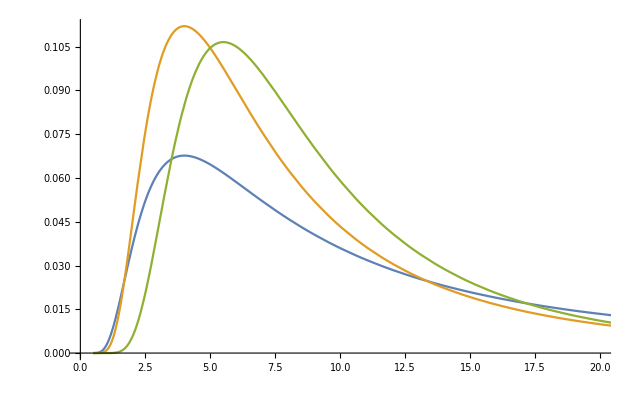

```mathematica
Plot[{1/tau (8/tau) Exp[-8/tau],1/tau(12/tau)^2 Exp[-12/tau],1/(2!tau)(22/tau)^3 Exp[-22/tau]},{tau,.5,100},PlotRange->{{0,20},All}]
```

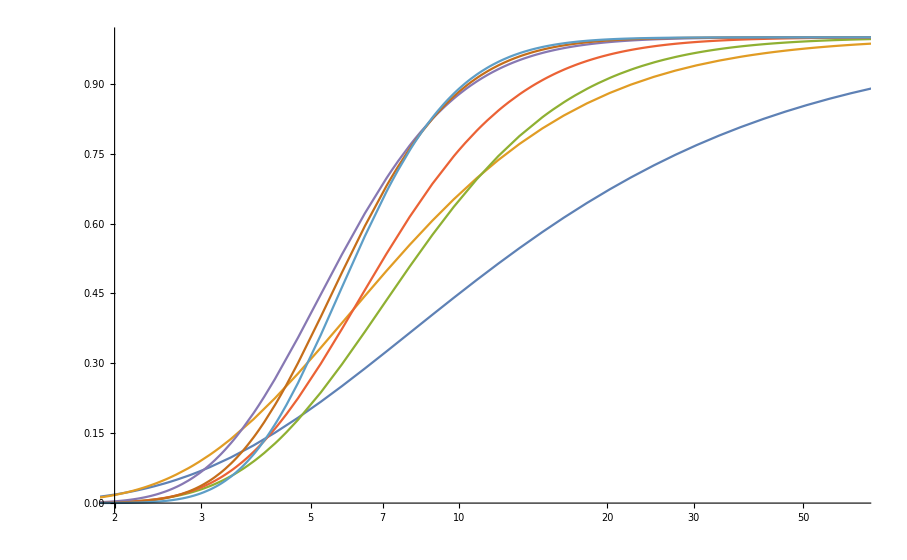

```mathematica
LogLinearPlot[Evaluate[Table[(Integrate[1/(i-1)! 1/tau (#[[i]]/tau)^i Exp[-#[[i]]/tau],{tau,0,t}]//Factor)[[1]],{i,1,Length@#}]&[{8,12,21,25,26,33,40}]],{t,1,160},PlotRange->{{2,64},All}]
```

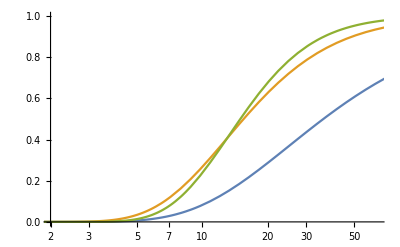

```mathematica
LogLinearPlot[Evaluate[Table[(Integrate[1/(i-1)! 1/tau (#[[i]]/tau)^i Exp[-#[[i]]/tau],{tau,0,t}]//Factor)[[1]],{i,1,Length@#}]&[{25,26,40}]],{t,1,160},PlotRange->{{2,64},All}]
```

```mathematica
NSolve[(ⅇ^(-22/t) (242+22 t+t^2))/t^2==#,t,Reals]&/@{.25,.75}
```

{{{t→5.61167}},{{t→12.7366}}}

```mathematica
i=4;
Evaluate[Table[(Integrate[1/(i-1)! 1/tau (#[[i]]/tau)^i Exp[-#[[i]]/tau],{tau,0,t}]//Factor)[[1]],{i,1,Length@#}]&[{8,12,21,25,26,33}]]
```

{ⅇ^(-8/t),(ⅇ^(-12/t) (12+t))/t,(ⅇ^(-21/t) (441+42 t+2 t^2))/(2 t^2),(ⅇ^(-25/t) (15625+1875 t+150 t^2+6 t^3))/(6 t^3),(ⅇ^(-26/t) (57122+8788 t+1014 t^2+78 t^3+3 t^4))/(3 t^4),(ⅇ^(-33/t) (13045131+1976535 t+239580 t^2+21780 t^3+1320 t^4+40 t^5))/(40 t^5)}

```mathematica
Integrate[1/(3!tau)(25/tau)^4 Exp[-25/tau]1/tau Exp[-t/tau],{tau,0,Infinity}]
```

ConditionalExpression[1562500/(25+t)^5,Re[t]>-25]

```mathematica
Integrate[1562500/(25+t)^5,{t,0,T}]
```

ConditionalExpression[1562500 (1/1562500-1/(4 (25+T)^4)),Re[T]>-25||T∉ℝ]

```mathematica
31944 (1/31944-1./(3 (22+T)^3))/.T->#&/@Range[7]
```

{0.124846,0.229745,0.318528,0.394174,0.459026,0.514942,0.56341}

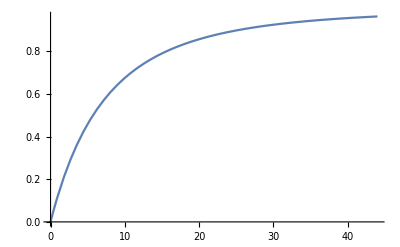

```mathematica
Plot[31944 (1/31944-1/(3 (22+T)^3)),{T,0,44}]
```

```mathematica
1562500 (1/1562500-1./(4 (25+T)^4))/.T->#&/@Range[2,12,2]
```

{0.26497,0.447709,0.577026,0.670615,0.739692,0.791573}

```mathematica
10*10/.000001(Exp[-10*3]-Exp[-10.000001*3])
```

2.80728×10^-11

```mathematica
3*10^2*Exp[-10*3.]
```

2.80729×10^-11

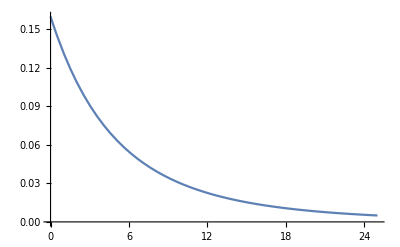

```mathematica
Plot[1562500/(25+t)^5,{t,0,25}]
```

```mathematica
GrayLevel[.8]
```

GrayLevel[0.8]

```mathematica
LogLinearPlot[Evaluate[(Table[1/(i-1)! (#[[i]]/tau)^i Exp[-#[[i]]/tau],{i,1,Length@#}]&@{8,12,21,33,42,43,47,49,51,51,63,91,92,97,98})],{tau,1,50}]
```

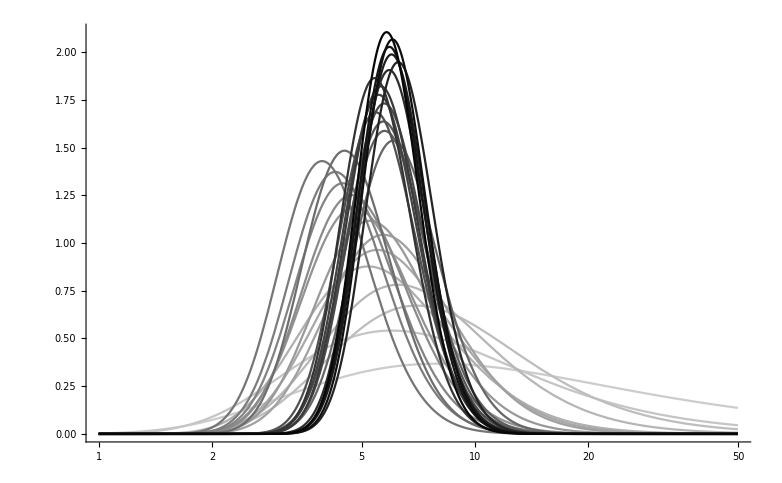

```mathematica
LogLinearPlot[Evaluate[Table[1/(i-1)! (#[[i]]/tau)^i Exp[-#[[i]]/tau],{i,1,Length@#}]],{tau,1,50},PlotStyle->GrayLevel/@Mod[Range[.8,0,-1 .8/Length[#]],1],PlotRange->All]&@{8,12,21,25,26,33,40,42,43,47,49,51,51,63,91,92,97,98,109,111,118,119,136,150,150,154,163,163}
```

```mathematica
now=163;
```

```mathematica
plot[ls_,s_,e_]:=LogLinearPlot[Evaluate[(Table[1/(#[[2,i]]-1)! (#[[1,i]]/tau)^#[[2,i]]Exp[-#[[1,i]]/tau],{i,1,Length@#[[1]]}]&@
{ls~Join~{now},Range[Length@ls]~Join~{Length@ls}})],{tau,s,e},PlotRange->All]
```

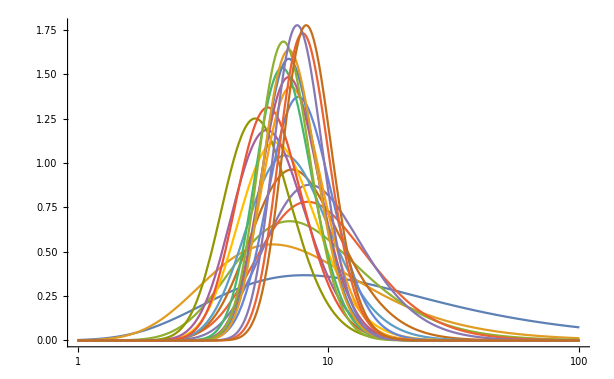

```mathematica
(* BBH *)
plot[{8,12,21,33,42,43,47,49,51,51,63,91,92,97,98,111,118,119,150,150},1,100]
```

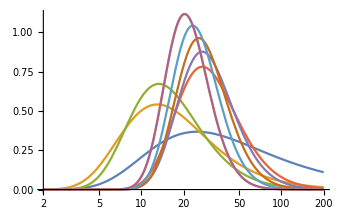

```mathematica
(* non BBH *)
plot[{25,26,40,109,136,154,163,163},2,200]
```

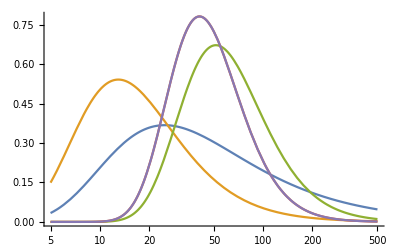

```mathematica
(* BNS *)
plot[{25,26,154,163},5,500]
```

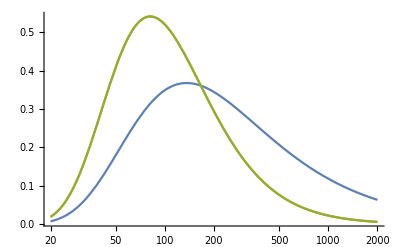

```mathematica
(* NSBH *)
plot[{136,163},20,2000]
```

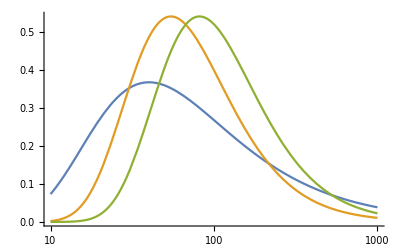

```mathematica
(* Terr *)
plot[{40,109},10,1000]
```

```mathematica
Integrate[1/(4!tau)(32/tau)^5 Exp[-32/tau]1/tau Exp[-t/tau],{tau,0,Infinity}]
```

ConditionalExpression[167772160/(32+t)^6,Re[t]>-32]

```mathematica
Integrate[167772160/(32+t)^6,{t,0,T}]
```

ConditionalExpression[167772160 (1/167772160-1/(5 (32+T)^5)),Re[T]>-32||T∉ℝ]

```mathematica
167772160 (1/167772160-1/(5 (32+T)^5))/.T->#&/@Range[7]//N
```

{0.142606,0.261492,0.361134,0.445071,0.516116,0.576521,0.628099}

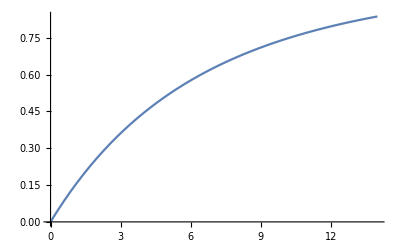

```mathematica
Plot[167772160 (1/167772160-1/(5 (32+T)^5)),{T,0,14}]
```

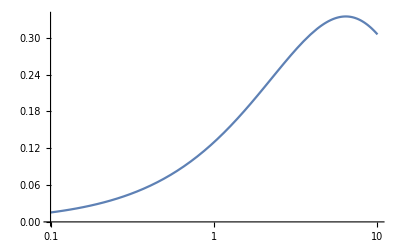

```mathematica
LogLinearPlot[167772160/(32+t)^6 t,{t,.1,10}]
```

```mathematica
?InverseCDF
```

InverseCDF[dist,q] gives the inverse of the cumulative distribution function for the distribution dist as a function of the variable q.

```mathematica
CDF[NormalDistribution[],-1.5]
```

0.0668072

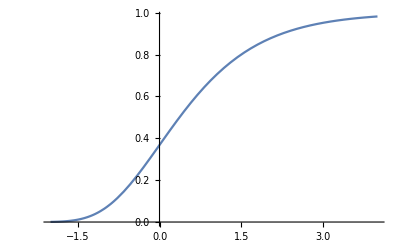

```mathematica
Plot[Exp[-Exp[-x]],{x,-2,4},PlotRange->All]
```

```mathematica
Table[1/(i-1)! (#[[i]]/tau)^i Exp[-#[[i]]/tau],{i,1,Length@#}]&@{40}
```

{(40 ⅇ^(-40/tau))/tau}

```mathematica
Integrate[(40 ⅇ^(-40/tau))/tau^2,{tau,t1,t2}]
```

ConditionalExpression[40 (-1/40 ⅇ^(-40/t1)+ⅇ^(-40/t2)/40),(t1/(t1-t2)≠0&&Re[t1/(-t1+t2)]≥0)||Re[t1/(t1-t2)]>1||t1/(t1-t2)∉ℝ]

```mathematica
40 (-1/40 ⅇ^(-40/t1)+ⅇ^(-40/t2)/40)//Simplify
```

-ⅇ^(-40/t1)+ⅇ^(-40/t2)

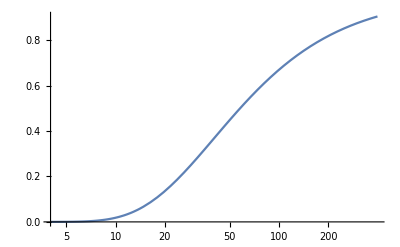

```mathematica
LogLinearPlot[Exp[-40/t],{t,4,400}]
```